```mathematica
c={
{"C3","C4","E4","G4","C5","E5","G5"},(*1^*)
{"A2","A3","C4","E4","A4","C5","E5"},(*6*)
{"F2","F3","A3","C4","F4","A4","C5"},(*4*)
{"G2","G3","B3","D4","G4","B4","D5"}    (*5*)
};
```

```mathematica
(*把音符一分为二*)
sl[array_,con_]:=If[con,
{SoundNote[array⟦1⟧,{array⟦2,1⟧,array⟦2,2⟧-1/4},array⟦3⟧],

SoundNote[array⟦1⟧,{array⟦2,1⟧+1/4,array⟦2,2⟧},array⟦3⟧]},
SoundNote[array⟦1⟧,array⟦2⟧,array⟦3⟧]
]
```

```mathematica
Accomp[st_,slshli_,moveli_]:=Table[{
Table[SoundNote[c⟦n,1⟧,{8s+2(n-1),8s+2n},"Violin"],{n,1,4}],
Table[sl[{
(*转位*) If[MemberQ[moveli,m],c⟦n,3;;5⟧,c⟦n,1;;4⟧]
,{8s+2(n-1)+(m-1)/2,8s+2(n-1)+m/2},"Piano"},MemberQ[slshli,m]],{n,1,4},{m,1,4}]
},{s,0,st-1}]
```

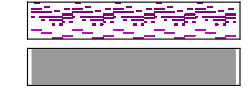

```mathematica
Sound[Flatten[Accomp[4,{2},{2,3}]]]
```

```mathematica
cs={
{"G4","C5","E5","G5","C6","E6","G6"},(*1^*)
{"E4","A4","C5","E5","A5","C6","E6"},(*6*){"C4","F4","A4","C5","F5","A5","C6"},(*4*){"D4","G4","B4","D5","G5","B5","D6"}    (*5*)
};
```

```mathematica
Gen[num_,st_]:=(g=RealDigits[num,10,4*st+4]⟦1⟧;
Sound[Flatten[{Accomp[st,{2},{2,3}],
Table[SoundNote[cs⟦Mod[Ceiling[i/4],4,1],
(*主旋律每小节用相同序列*) Mod[g⟦Mod[i,4,1]+Floor[i/16]*4⟧,6]+2⟧,{(i-1)/2,i/2},"Violin"],{i,1,16*st}]
}]]
)
```

```mathematica
Table[
(*主旋律每小节用相同序列*) Mod[i,4,1]+Floor[i/16]*4,{i,1,16*8}]
```

{1,2,3,4,1,2,3,4,1,2,3,4,1,2,3,8,5,6,7,8,5,6,7,8,5,6,7,8,5,6,7,12,9,10,11,12,9,10,11,12,9,10,11,12,9,10,11,16,13,14,15,16,13,14,15,16,13,14,15,16,13,14,15,20,17,18,19,20,17,18,19,20,17,18,19,20,17,18,19,24,21,22,23,24,21,22,23,24,21,22,23,24,21,22,23,28,25,26,27,28,25,26,27,28,25,26,27,28,25,26,27,32,29,30,31,32,29,30,31,32,29,30,31,32,29,30,31,36}

```mathematica
SetDirectory[NotebookDirectory[]];
Export["pi.mp3",Gen[π,8]]
Export["e.mp3",Gen[E,8]]
Export["sqrt2.mp3",Gen[√2,8]]
```

pi.mp3

e.mp3

sqrt2.mp3